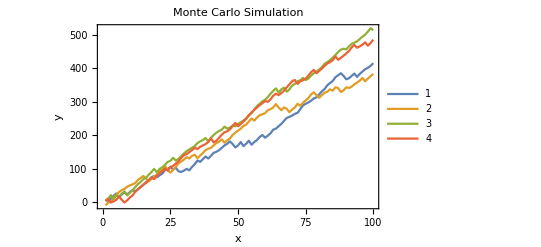

```mathematica
list=  {{}, {}, {}, {}};
arr = RandomInteger[{1, 6},{4, 2, 100}];
For[j = 1, j <= 4,j++,
sum = 0;
For[i = 1,i <= 100, i++, 
If[arr[[j, 1,i]] == arr[[j, 2, i]], sum -= (arr[[j, 1,i]] + arr[[j, 2,i]]), sum += (arr[[j, 1,i]] + arr[[j, 2,i]])];
list[[j]] = Append[list[[j]], sum]
];
]
ListPlot[list, Joined-> True, PlotLegends->Automatic, Frame-> True, PlotLabel->"Monte Carlo Simulation", FrameLabel->{"x", "y"}]
```

```mathematica
eqn1 = (e'[t] == -(304 * k * e[t]) /(15 * a[t]^4 * (1 - e[t]^2)^(5/2))*(1 + 121 e[t]^2/304))
eqn2 = (a'[t] == -64 k/(5 a[t]^3 (1 - e[t]^2)^(7/2))(1 + 73e[t]^2/24 + 37 e[t]^4/96))
```

e'[t]==-(304 k e[t] (1+(121 e[t]^2)/304))/(15 a[t]^4 (1-e[t]^2)^(5/2))

a'[t]==-(64 k (1+(73 e[t]^2)/24+(37 e[t]^4)/96))/(5 a[t]^3 (1-e[t]^2)^(7/2))

```mathematica
DSolve[{eqn1, eqn2}, {a[t], e[t]}, t]
```

$Aborted